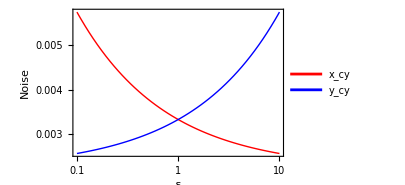

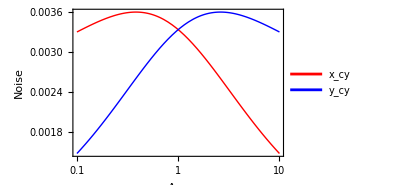

```mathematica
(*
This is part of the manuscript titled "Feedback-mediated circulation and persistence of stochastic fluctuations in gene
regulatory circuits" ;

Correspondence with the paper;

Please note ;
1. The four TNF motifs: Double positive feedback (++), Double negative feedback (--), Negative positive feedback (-+) and Positive negative feedback (+-);
2. αx and αy are production rates of X and Y;
3. βx and βy are degradation rates of X and Y;
4. fx=αx*gx, fy=αy*gy are the Hill functions with Hill coefficient=1;
5. xdot and ydot are the dynamical equations of X and Y;
6. xav=<x>, yav=<y> ;
7. fxyp = ∂fx/∂y and fyxp=∂fy/∂x are steady-state regulatory sensitivities;
8. G = H (feedback gain);
9. τxy and τyx are time-averaging factors;
9. δ is feedback strength and aτ is time-scale asymmetry;
10. The noise decomposition terms - intrinsic noise(xint,yint), extrinsic noise(xext,yext) and cyclic noise(xcy,ycy) are analytically derived from solving the Lyapunov equation to get the moments and then defining noise as dimensionless squared coefficient of variation;
11. xcy and ycy are the cyclic noise terms of X and Y, respectively;
12. The data is exported and plotted in another software 
====================================================================== 
*)

(* Double Positive Feedback *)

gx=y/(y+Kyx);gy=x/(x+Kxy); (*Functions*)

xdot=αx*gx-βx*x;
ydot=αy*gy-βy*y;

sol=Solve[{xdot==0,ydot==0},{x,y}];

(*fixed points*)
xav=x/.sol[[2,1]];
yav=y/.sol[[2,2]];

fx=αx*gx; fy=αy*gy;

fxyp=αx*Kyx/(yav+Kyx)^2;fyxp=αy*Kxy/(xav+Kxy)^2;(*Derivative of functions fx, fy*)

(*Time averaging factor*)
τyx=βy/(βx+βy);
τxy=βx/(βx+βy);

G=(fxyp*fyxp)/(βx*βy); (*Feedback gain*)

(*Noise Decomposition*)
xint=1/xav;    (* intrinsic noise *)
xext=(fxyp^2 yav)/(βx(βx+βy)xav^2)*1/(1-G); (*extrinsic noise*)
xcy =τyx* G/(1-G)*xint; (*cyclic noise*)
xtot=xint+xext+xcy;

yint=1/yav;
yext=(fyxp^2 xav)/(βy(βx+βy)yav^2)*1/(1-G);
ycy =τxy* G/(1-G)*yint;
ytot=yint+yext+ycy;

(*========================Data Extraction formatting===============================*)
toEString[dat_]:=If[dat==0.,"0.0000000000000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];
(*================================================================================*)

(*Parameters*)
αx=10; αy=10;
βx=0.1; βy=0.1;
Kyx=50/Sqrt[δ]; Kxy=50*Sqrt[δ];

δi=0.1;δf=10;

p4=LogLinearPlot[{xcy,ycy},{δ,δi,δf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"δ","Noise"},ImageSize->300,PlotLegends->{"x_cy","y_cy"},PlotRange->All]
t4=Table[{δ,xcy,ycy},{δ,δi,δf,0.1}];
tp4=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@t4];
(*Export["D:\\nashitarahman\\DP4cy.dat",tp4,"FieldSeparators"->"    "];*)

Clear[βx,βy,Kxy,Kyx];

(*Parameters*)
βx=0.1*Sqrt[aτ]; βy=0.1/Sqrt[aτ];
Kyx=50; Kxy=50;

aτi=0.1;aτf=10;

p8=LogLinearPlot[{xcy,ycy},{aτ,aτi,aτf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"A_τ","Noise"},ImageSize->300,PlotLegends->{"x_cy","y_cy"},PlotRange->All]
t8=Table[{aτ,xcy,ycy},{aτ,aτi,aτf,0.01}];
tp8=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@t8];
(*Export["D:\\nashitarahman\\DP8cy.dat",tp8,"FieldSeparators"->"    "];*)

Quit[];
```

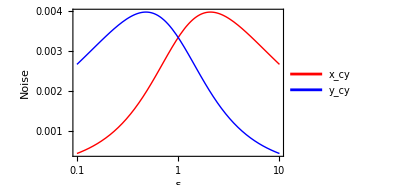

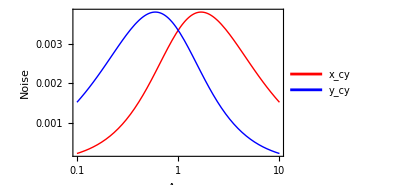

```mathematica
(*Double negative feedback*)
gx=Kyx/(y+Kyx);gy=Kxy/(x+Kxy);

xdot=αx*gx-βx*x;
ydot=αy*gy-βy*y;

sol=Solve[{xdot==0,ydot==0},{x,y}];

xav=x/.sol[[1,1]];
yav=y/.sol[[1,2]];

fxyp=-αx*Kyx/(yav+Kyx)^2;fyxp=-αy*Kxy/(xav+Kxy)^2;

τyx=βy/(βx+βy);
τxy=βx/(βx+βy);
G=fxyp*fyxp/(βx*βy);

xint=1/xav;
xext=(fxyp^2 yav)/(βx(βx+βy)xav^2)*1/(1-G);
xcy =τyx* G/(1-G)*xint;
xtot=xint+xext+xcy;

yint=1/yav;
yext=(fyxp^2 xav)/(βy(βx+βy)yav^2)*1/(1-G);
ycy =τxy* G/(1-G)*yint;
ytot=yint+yext+ycy;

(*========================Data Extraction formatting===============================*)
toEString[dat_]:=If[dat==0.,"0.0000000000000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];
(*================================================================================*)

(*Parameters*)
αx=10; αy=10;
βx=0.1; βy=0.1;
Kyx=50/Sqrt[δ]; Kxy=50*Sqrt[δ];

δi=0.1;δf=10;

p4=LogLinearPlot[{xcy,ycy},{δ,δi,δf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"δ","Noise"},ImageSize->300,PlotLegends->{"x_cy","y_cy"},PlotRange->All]
t4=Table[{δ,xcy,ycy},{δ,δi,δf,0.1}];
tp4=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@t4];
(*Export["D:\\nashitarahman\\DN4cy.dat",tp4,"FieldSeparators"->"    "];*)

Clear[βx,βy,Kxy,Kyx];

(*Parameters*)
βx=0.1*Sqrt[aτ]; βy=0.1/Sqrt[aτ];
Kyx=50; Kxy=50;

aτi=0.1;aτf=10;

p8=LogLinearPlot[{xcy,ycy},{aτ,aτi,aτf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"A_τ","Noise"},ImageSize->300,PlotLegends->{"x_cy","y_cy"},PlotRange->All]
t8=Table[{aτ,xcy,ycy},{aτ,aτi,aτf,0.01}];
tp8=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@t8];
(*Export["D:\\nashitarahman\\DN8cy.dat",tp8,"FieldSeparators"->"    "];*)

Quit[];
```

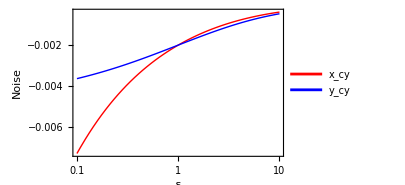

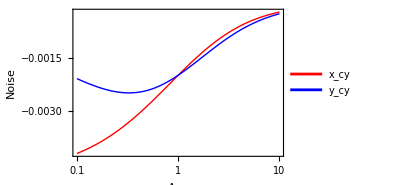

```mathematica
(*Negative positive feedback*)

gx=y/(y+Kyx);gy=Kxy/(x+Kxy);

xdot=αx*gx-βx*x;
ydot=αy*gy-βy*y;

sol=Solve[{xdot==0,ydot==0},{x,y}];

xav=x/.sol[[2,1]];
yav=y/.sol[[2,2]];

fxyp=αx*Kyx/(yav+Kyx)^2;fyxp=-αy*Kxy/(xav+Kxy)^2;

τyx=βy/(βx+βy);
τxy=βx/(βx+βy);
G=fxyp*fyxp/(βx*βy);

xint=1/xav;
xext=(fxyp^2 yav)/(βx(βx+βy)xav^2)*1/(1-G);
xcy =τyx* G/(1-G)*xint;
xtot=xint+xext+xcy;

yint=1/yav;
yext=(fyxp^2 xav)/(βy(βx+βy)yav^2)*1/(1-G);
ycy =τxy* G/(1-G)*yint;
ytot=yint+yext+ycy;

(*========================Data Extraction formatting===============================*)
toEString[dat_]:=If[dat==0.,"0.0000000000000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];
(*================================================================================*)

(*Parameters*)
αx=10; αy=10;
βx=0.1; βy=0.1;
Kyx=50/Sqrt[δ]; Kxy=50*Sqrt[δ];

δi=0.1;δf=10;

p4=LogLinearPlot[{xcy,ycy},{δ,δi,δf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"δ","Noise"},ImageSize->300,PlotLegends->{"x_cy","y_cy"},PlotRange->All]
t4=Table[{δ,xcy,ycy},{δ,δi,δf,0.01}];
tp4=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@t4];
(*Export["D:\\nashitarahman\\NP4cy.dat",tp4,"FieldSeparators"->"    "];*)

Clear[βx,βy,Kxy,Kyx];

(*Parameters*)
βx=0.1*Sqrt[aτ]; βy=0.1/Sqrt[aτ];
Kyx=50; Kxy=50;

aτi=0.1;aτf=10;

p8=LogLinearPlot[{xcy,ycy},{aτ,aτi,aτf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"A_τ","Noise"},ImageSize->300,PlotLegends->{"x_cy","y_cy"},PlotRange->All]
t8=Table[{aτ,xcy,ycy},{aτ,aτi,aτf,0.01}];
tp8=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@t8];
(*Export["D:\\nashitarahman\\NP8cy.dat",tp8,"FieldSeparators"->"    "];*)

Quit[];
```

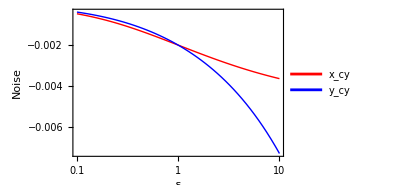

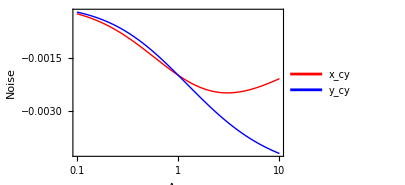

```mathematica
(*Positive negative feedback*)
gx=Kyx/(y+Kyx);gy=x/(x+Kxy);

xdot=αx*gx-βx*x;
ydot=αy*gy-βy*y;

sol=Solve[{xdot==0,ydot==0},{x,y}];

xav=x/.sol[[2,1]];
yav=y/.sol[[2,2]];

fxyp=-αx*Kyx/(yav+Kyx)^2;fyxp=αy*Kxy/(xav+Kxy)^2;

τyx=βy/(βx+βy);
τxy=βx/(βx+βy);
G=fxyp*fyxp/(βx*βy);

xint=1/xav;
xext=(fxyp^2 yav)/(βx(βx+βy)xav^2)*1/(1-G);
xcy =τyx* G/(1-G)*xint;
xtot=xint+xext+xcy;

yint=1/yav;
yext=(fyxp^2 xav)/(βy(βx+βy)yav^2)*1/(1-G);
ycy =τxy* G/(1-G)*yint;
ytot=yint+yext+ycy;

(*========================Data Extraction formatting===============================*)
toEString[dat_]:=If[dat==0.,"0.0000000000000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];
(*================================================================================*)

(*Parameters*)
αx=10; αy=10;
βx=0.1; βy=0.1;
Kyx=50/Sqrt[δ]; Kxy=50*Sqrt[δ];

δi=0.1;δf=10;

p4=LogLinearPlot[{xcy,ycy},{δ,δi,δf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"δ","Noise"},ImageSize->300,PlotLegends->{"x_cy","y_cy"},PlotRange->All]
t4=Table[{δ,xcy,ycy},{δ,δi,δf,0.01}];
tp4=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@t4];
(*Export["D:\\nashitarahman\\PN4cy.dat",tp4,"FieldSeparators"->"    "];*)

Clear[βx,βy,Kxy,Kyx];

(*Parameters*)
βx=0.1*Sqrt[aτ]; βy=0.1/Sqrt[aτ];
Kyx=50; Kxy=50;

aτi=0.1;aτf=10;

p8=LogLinearPlot[{xcy,ycy},{aτ,aτi,aτf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"A_τ","Noise"},ImageSize->300,PlotLegends->{"x_cy","y_cy"},PlotRange->All]
t8=Table[{aτ,xcy,ycy},{aτ,aτi,aτf,0.01}];
tp8=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@t8];
(*Export["D:\\nashitarahman\\PN8cy.dat",tp8,"FieldSeparators"->"    "];*)

Quit[];
```